```mathematica
If[NumberQ[bQdef],None,Quit[]];
```

# P13 functions

Alejandro Aviles (avilescervantes@gmail.com)
Compute P13 functions for HS models and LCDM

```mathematica
SetDirectory[NotebookDirectory[]]
dir=SetDirectory[NotebookDirectory[]]<>"/";
Print["Running P13 functions"];
<<0_params.m
If[NumberQ[bQdef],None,<<0_folders.m];
```

/home/waco/Dropbox/RSDMG/SPT/AfterPaper/sMGPT_nb

Running P13 functions

## General parameters

```mathematica
PSLT=Import[outputdir<>"/PSL_"<>suffix<>".dat"];
PSL=Interpolation[PSLT];
fkTh=Import[outputdir<>"/fk_"<>suffix<>".dat"];
f0=fkTh[[2,2]];
Print["f(k=0)=",f0];
(*If[bLCDM==1,fk[k_]:=f0,fk=Interpolation[fkTh]];*)(*Assuming the MG model f[k=0]=f_LCDM.Does not work in DGP*)
fk=Interpolation[fkTh]

sizepk=Dimensions[PSLT][[1]];
kinMin=PSLT[[1,1]];
kinMax=PSLT[[sizepk,1]];
Print["input PS points = ",sizepk,", kmin = ",PSLT[[1,1]],", kmax = ",PSLT[[sizepk,1]]]
fourpi2=4.Pi^2;
```

f(k=0)=0.733327

InterpolatingFunction[{{0.00001, 521.888}}, <>]

input PS points = 890, kmin = 0.00001, kmax = 521.888

## General functions (modify here for other models)

```mathematica
OmM[eta_]:=1/(1+(1-om)/om Exp[3eta]);
H[eta_]:=√(om Exp[-3eta]+(1-om));

f1[eta_]:=(2.-3./(2.(1.+(1-om)/om Exp[3.eta])));
f2[eta_]:=3./(2.(1.+(1-om)/om Exp[3.eta]));
invH0 =2997.92458 ;(* H_0^-1 in Mpc/h units *)


(* MODEL DEPENDENT FUNCTIONS *)
beta2=1/6;
nHS=1;
wBD=0;
mass[eta_]:=1/invH0(1/(2 fR0))^(1/2)(om Exp[-3 eta]+4(1-om))^((2+nHS)/2)/(om+4(1-om))^((1+nHS)/2);
mu[eta_,k_]:=1+(2beta2 k^2)/(k^2+Exp[2 eta] mass[eta]^2) ; (*mu is from A(k) = 3/2 Subscript[Ω, m] H^2 μ *)
M1[eta_]:=3 mass[eta]^2
M2[eta_]:=Sc(9./4)/invH0^2(1/fR0)^2(om Exp[-3. eta]+4.(1-om))^5/(om+4(1-om))^4;
M3[eta_]:=Sc(45./8)/invH0^2(1/fR0)^3(om Exp[-3. eta]+4.(1-om))^7/(om+4(1-om))^6;

A0[eta_]:=1.5(OmM[eta] H[eta]^2)/invH0^2;

(* Derived FUNCTIONS *)

PiF[eta_,k_]:=k^2/Exp[2. eta]+mass[eta]^2;
KFL[eta_,kf_,k1_,k2_]:=0.5((kf^2-k1^2-k2^2)^2)/(k1^2 k2^2)(  mu[eta,k1]+mu[eta,k2]-2.)+0.5(kf^2-k1^2-k2^2)/k1^2( mu[eta,k1]-1.)+0.5(kf^2-k1^2-k2^2)/k2^2( mu[eta,k2]-1.) ;

KFL2[eta_,x_,k_,p_]:=2 x^2 (mu[eta,k]+mu[eta,p]-2.)+(p x)/k(mu[eta,k]-1.)+(k x)/p(mu[eta,p]-1.);
JFL[eta_,x_,k_,p_]:=9./(2.A0[eta])KFL2[eta,x,k,p]PiF[eta,k]PiF[eta,p];

kplusp[x_,k_,p_]:=Sqrt[k^2+p^2+2. k p x];

KFL3[eta_,x_,k_,p_]:=KFL[eta,kplusp[x,k,p],k,p];
```

## Equations

```mathematica
Clear[x,k,p]
source2a[eta_,x_,k_,p_]:=f2[eta] mu[eta,kplusp[x,k,p]]
source2b[eta_,x_,k_,p_]:=f2[eta] (mu[eta,k]+mu[eta,p]-mu[eta,kplusp[x,k,p]])
source2FL[eta_,x_,k_,p_]:=f2[eta] (mu[eta,kplusp[x,k,p]]*(p/k+k/p)*x -k x/p mu[eta,k]-p x/k mu[eta,p])
source2dI[eta_,x_,k_,p_]:=Sc 1/6((OmM[eta]H[eta])/(Exp[eta]invH0))^2(kplusp[x,k,p]^2 M2[eta])/(PiF[eta,kplusp[x,k,p]]PiF[eta,k]PiF[eta,p])

sourceD2[eta_,x_,k_,p_]:=source2a[eta,x,k,p]-source2b[eta,x,k,p] x^2+source2FL[eta,x,k,p]-Sc source2dI[eta,x,k,p]



source3I[eta_,x_,k_,p_]:=(f2[eta] (mu[eta,p]+ mu[eta,kplusp[x,k,p]]-mu[eta,k])D2f[eta]Dpp[eta]+sourceD2[eta,x,k,p]Dpk[eta]Dpp[eta]Dpp[eta])(1.-x^2)/(1.+(p/k)^2+2 p/k x) +(f2[eta] (mu[eta,p]+ mu[eta,kplusp[-x,k,p]]-mu[eta,k])D2mf[eta]Dpp[eta]+sourceD2[eta,-x,k,p]Dpk[eta]Dpp[eta]Dpp[eta])(1.-x^2)/(1.+(p/k)^2-2 p/k x)

source3IIplus[eta_,x_,k_,p_]:=-f2[eta](mu[eta,p]+mu[eta,kplusp[x,k,p]]-2mu[eta,k])Dpp[eta](D2f[eta]+Dpk[eta]Dpp[eta] x^2 )-f2[eta](mu[eta,kplusp[x,k,p]]-mu[eta,k])Dpk[eta]Dpp[eta]Dpp[eta]-f2[eta]((mu[eta,kplusp[x,k,p]]*(p/k+k/p)*x-k x/p mu[eta,k]-p x/k mu[eta,p]))Dpk[eta]Dpp[eta]Dpp[eta]


source3II[eta_,x_,k_,p_]:=source3IIplus[eta,x,k,p]+source3IIplus[eta,-x,k,p]




sourceFL3Plus[eta_,x_,k_,p_]:=f2[eta]( ((p^2+p k x)/(k^2+p^2+2. p k x))(mu[eta,p]-mu[eta,k])D2f[eta]Dpp[eta]+ ((p^2+p k x)/p^2)(mu[eta,kplusp[x,k,p]]-mu[eta,k])( D2f[eta]Dpp[eta]+(1+x^2)Dpk[eta]Dpp[eta]Dpp[eta] )+(((p^2+k^2) x^2)/p^2+((p^2+k^2) x)/(p k))(mu[eta,kplusp[x,k,p]]-mu[eta,k])Dpk[eta]Dpp[eta]Dpp[eta])


sourceFL3[eta_,x_,k_,p_]:=sourceFL3Plus[eta,x,k,p]+sourceFL3Plus[eta,-x,k,p]



sourceSc2plus[eta_,x_,k_,p_]:=(((OmM[eta] H[eta])/invH0)^2(M2[eta] kplusp[x,k,p]^2 Exp[-2. eta])/(6PiF[eta,kplusp[x,k,p]]PiF[eta,k]PiF[eta,p]))Dpk[eta]Dpp[eta]Dpp[eta]+-f2[eta] M1[eta]/(3PiF[eta,k]) ((p^2+3 k p x+2 k^2 x^2)/kplusp[x,k,p]^2)(mu[eta,kplusp[x,k,p]]-1.)((2.A0[eta])/3 M2[eta]/(3PiF[eta,k]PiF[eta,p]))Dpk[eta]Dpp[eta]Dpp[eta];

sourceSc2[eta_,x_,k_,p_]:=sourceSc2plus[eta,x,k,p]+sourceSc2plus[eta,-x,k,p]




K3dI[eta_,x_,k_,p_]:=2((OmM[eta] H[eta])/invH0)^2 M2[eta]/(PiF[eta,k] PiF[eta,0])+1/3.((OmM[eta]^3 H[eta]^4)/invH0^4)(M3[eta]-(M2[eta](M2[eta]+JFL[eta,-1,p,p](3+2wBD)))/PiF[eta,0])1/(PiF[eta,p]^2 PiF[eta,k])+((OmM[eta] H[eta])/invH0)^2 M2[eta]/(PiF[eta,p] PiF[eta,kplusp[x,k,p]])(1+x^2+D2f[eta]/(Dpk[eta]Dpp[eta]))+1/3.((OmM[eta]^3 H[eta]^4)/invH0^4)(M3[eta]-(M2[eta](M2[eta]+JFL[eta,x,k,p](3+2wBD)))/PiF[eta,kplusp[x,k,p]])1/(PiF[eta,p]^2 PiF[eta,k])+ ((OmM[eta] H[eta])/invH0)^2 M2[eta]/(PiF[eta,p] PiF[eta,kplusp[-x,k,p]])(1+x^2+D2mf[eta]/(Dpk[eta]Dpp[eta]))+1/3.((OmM[eta]^3 H[eta]^4)/invH0^4)(M3[eta]-(M2[eta](M2[eta]+JFL[eta,-x,k,p](3+2wBD)))/PiF[eta,kplusp[-x,k,p]])1/(PiF[eta,p]^2 PiF[eta,k])


sourcedI3[eta_,x_,k_,p_]:=-Sc k^2/Exp[2.eta] 1./(6PiF[eta,k])K3dI[eta,x,k,p]Dpk[eta]Dpp[eta]Dpp[eta];
```

## Diff equations

```mathematica
etainI=-4;
etafI=0.1;
etaini=etainI;
etafinal=0;

Dplusi=Exp[etaini];
dDplusi=Exp[etaini];

D2plusi=3.Exp[2etaini]/7.(1.-x^2);
dD2plusi=6.Exp[2etaini]/7.(1.-x^2);
D3symmi=5./7. Exp[3.etaini]/9.((1.-x^2)/(1.+(p/k)^2+2 p/k x)+(1.-x^2)/(1.+(p/k)^2-2 p/k x))(1.-x^2);
dD3symmi=15./7. Exp[3etaini]/9.((1.-x^2)/(1.+(p/k)^2+2 p/k x)+(1.-x^2)/(1.+(p/k)^2-2 p/k x))(1.-x^2);


eqD3symm=D3symmf''[eta] +f1[eta]D3symmf'[eta]-f2[eta] mu[eta,k]D3symmf[eta]==source3I[eta,x,k,p]+source3II[eta,x,k,p]+sourceFL3[eta,x,k,p]+ sourcedI3[eta,x,k,p]+ sourceSc2[eta,x,k,p];
eqD2p=D2f''[eta] +f1[eta]D2f'[eta]-f2[eta] mu[eta,kplusp[x,k,p]]D2f[eta]==sourceD2[eta,x,k,p]Dpk[eta]Dpp[eta];
eqD2m=D2mf''[eta] +f1[eta]D2mf'[eta]-f2[eta] mu[eta,kplusp[-x,k,p]]D2mf[eta]==sourceD2[eta,-x,k,p]Dpk[eta]Dpp[eta];
eqDpk=Dpk''[eta] +f1[eta]Dpk'[eta]-f2[eta] mu[eta,k]Dpk[eta]==0;
eqDpp=Dpp''[eta] +f1[eta]Dpp'[eta]-f2[eta] mu[eta,p]Dpp[eta]==0;

sysD3symm=ParametricNDSolve[{eqD3symm,
eqD2p,eqD2m,eqDpk,eqDpp,D3symmf'[etaini]==dD3symmi,D3symmf[etaini]==D3symmi,D2f'[etaini]==dD2plusi,D2f[etaini]==D2plusi,D2mf'[etaini]==dD2plusi,D2mf[etaini]==D2plusi,Dpk'[etaini]==Exp[etaini],Dpk[etaini]==Exp[etaini],Dpp'[etaini]==Exp[etaini],Dpp[etaini]==Exp[etaini]},{D3symmf,D2f,D2mf,Dpk,Dpp},{eta,etainI,etafinal},{x,k,p}]

D3symm:=Evaluate[D3symmf/.sysD3symm]
D2:=Evaluate[D2f/.sysD3symm]
D2m:=Evaluate[D2mf/.sysD3symm]
xpreDk:=Evaluate[Dpk/.sysD3symm]
xpreDp:=Evaluate[Dpp/.sysD3symm]
xDk[k_]:=xpreDk[0.001,k,0.001]
xDp[p_]:=xpreDp[0.001,0.001,p]

D3[x_,k_,p_]:=D3symm[x,k,p][etaev]
D3prime[x_,k_,p_]:=D[D3symm[x,k,p][eta],eta]/.eta->etaev

AminusBx2[x_,k_,p_]:=(D2[x,k,p][etaev])/(3/7 xDk[k][etaev]xDp[p][etaev])
AminusBx2Prime[x_,k_,p_]:= D[(D2[x,k,p][eta])/(3/7 xDk[k][eta]xDp[p][eta]),eta]/.eta->etaev

(*NOTE THIS gamma3 and gamma3f are defined differently than the other NOTEBOOKS,there is an additional 21/5*)C3gamma3[x_,k_,p_]:=D3symm[x,k,p][etaev]/(xDk[k][etaev] xDp[p][etaev] xDp[p][etaev]);
C3gamma3f[x_,k_,p_]:=D3prime[x,k,p]/(xDk[k][etaev] xDp[p][etaev] xDp[p][etaev]) 1/(3 f0);


lcdmCF=C3gamma3[0.,0.00001,0.00001] 21/5
lcdmCFprime=C3gamma3f[0.,0.00001,0.00001] 21/5

AprimeLCDM=AminusBx2Prime[0,0.0001,0.0001] (*Large scales value.For f(R) this is LCDM*)
ALCDM=AminusBx2[0,0.0001,0.0001]  (*Large scales value.For f(R) this is LCDM*)
```

{D3symmf→ParametricFunction[<>],D2f→ParametricFunction[<>],D2mf→ParametricFunction[<>],Dpk→ParametricFunction[<>],Dpp→ParametricFunction[<>]}

1.0076

1.01762

0.00933312

1.00402

## Tables of k and p points

```mathematica
<<0_tables.m
```

Input kmin = 0.00001,  input kmax = 402.401

Output files log-k spaced: kmin = 0.001,  kmax = 1,  number of ks: 121

Inner integration pmin = 0.00001,  pmax = 16.,  number of ps: 183

## Plot linear PS

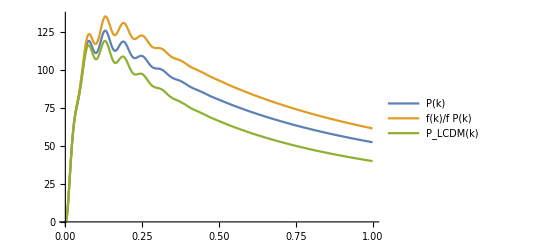

```mathematica
PSLCDMz0=Interpolation[Import[inputpk]];
Plot[{k^1.5PSL[k],k^1.5fk[k]/f0 PSL[k],k^1.5 PSL[0.0001]/PSLCDMz0[0.0001] PSLCDMz0[k]},{k,0.001,1},PlotLegends->{"P(k)","f(k)/f P(k)","P_LCDM(k)"}]
```

## INTEGRATE

## Define Kernels

```mathematica
If[PTkernels==1||PTkernels==2,bLCDMkernels=0,bLCDMkernels=1];
If[PTkernels==3||PTkernels==5,Clear[fk];fk[k_]:=f0];
If[PTkernels==5||PTkernels==6,ALCDM=1;AprimeLCDM=0];
If[PTkernels==5||PTkernels==6,lcdmCF =1;lcdmCFprime=1];

If[bLCDMkernels==0,AminusBx2h[x_,k_,p_]:=AminusBx2[x,k,p],AminusBx2h[x_,k_,p_]:=ALCDM (1-x^2)];
If[bLCDMkernels==0,AminusBx2Primeh[x_,k_,p_]:=AminusBx2Prime[x,k,p],AminusBx2Primeh[x_,k_,p_]:=AprimeLCDM (1.-x^2)];

kmpdk[x_,k_,p_]:=(1-x^2)^2/(1+(p/k)^2-2. p/k x);
(*C3gamma3LCDM[x_,k_,p_]  := 5/21lcdmCF             (kmpdk[x,k,p]+kmpdk[-x,k,p]) ;
C3gamma3fLCDM[x_,k_,p_]:= 5/21lcdmCFprime( kmpdk[x,k,p]+kmpdk[-x,k,p])  ;*) 
C3gamma3LCDM[x_,k_,p_]  := 2.*5/21lcdmCF             (kmpdk[x,k,p]) ;
C3gamma3fLCDM[x_,k_,p_]:= 2.*5/21lcdmCFprime( kmpdk[x,k,p])  ; 

If[bLCDMkernels==0,C3gamma3h[x_,k_,p_]:=C3gamma3[x,k,p],C3gamma3h[x_,k_,p_]:=C3gamma3LCDM[x,k,p]]
If[bLCDMkernels==0,C3gamma3fh[x_,k_,p_]:=C3gamma3f[x,k,p],C3gamma3fh[x_,k_,p_]:=C3gamma3fLCDM[x,k,p]]



C2=3/7;
F3K[k_,p_,x_,C3gamma3_,C3gamma3f_,gamma2evR_,gamma2fevR_,fk_,fp_,fkminusp_,f0_]:=1/6 C3gamma3+1/3 C2 ((k^2-k p x)k p x)/(p^2 (k^2+p^2-2p k x))gamma2evR -1/6 k^2/p^2 x^2;

G3K[k_,p_,x_,C3gamma3_,C3gamma3f_,gamma2evR_,gamma2fevR_,fk_,fp_,fkminusp_,f0_]:=1/2 C3gamma3f+2/3 C2 (k x)/p gamma2fevR+1/3 C2 fk/f0(k^2-k p x)/(k^2+p^2-2p k x)gamma2evR-1/6 k^2/p^2 x^2 fk/f0-1/3 C2(2gamma2fevR+gamma2evR fp/f0)(1-(k x-p)^2/(k^2+p^2-2p k x));



KP13dd[k_,r_,x_,C3gamma3_,C3gamma3f_,gamma2evR_,gamma2fevR_,fk_,fp_,fkminusp_,f0_]:=6 r^2F3K[k,k r,x,C3gamma3,C3gamma3f,gamma2evR,gamma2fevR,fk,fp,fkminusp,f0];
KP13tt[k_,r_,x_,C3gamma3_,C3gamma3f_,gamma2evR_,gamma2fevR_,fk_,fp_,fkminusp_,f0_]:=6 r^2G3K[k,k r,x,C3gamma3,C3gamma3f,gamma2evR,gamma2fevR,fk,fp,fkminusp,f0] fk/f0;
KP13dt[k_,r_,x_,C3gamma3_,C3gamma3f_,gamma2evR_,gamma2fevR_,fk_,fp_,fkminusp_,f0_]:=3 r^2G3K[k,k r,x,C3gamma3,C3gamma3f,gamma2evR,gamma2fevR,fk,fp,fkminusp,f0]+3r^2F3K[k,k r,x,C3gamma3,C3gamma3f,gamma2evR,gamma2fevR,fk,fp,fkminusp,f0] fk/f0;

sigma32PSLK[k_,p_,x_]:=105/16(  ((x-p/k )^2/(1+(p/k)^2-2. p/k  x)-1/3)(2/7(x^2-1/3)-4/21 )+8/63);
(*sigma32PSLK[k_,p_,x_]:=15/8  (x^2-1/3)((x-p/k )^2/(1+(p/k)^2-2. p/k  x)-1 )+5/6;*)
Ksigma32PSL[k_,r_,x_]:=r^2sigma32PSLK[k,k r,x];



RkernelsT[k_,r_,x_,C3gamma3_,C3gamma3f_,gamma2evR_,gamma2fevR_,fk_,fp_,fkminusp_,f0_]:={KP13dd[k,r,x,C3gamma3,C3gamma3f,gamma2evR,gamma2fevR,fk,fp,fkminusp,f0],KP13dt[k,r,x,C3gamma3,C3gamma3f,gamma2evR,gamma2fevR,fk,fp,fkminusp,f0],KP13tt[k,r,x,C3gamma3,C3gamma3f,gamma2evR,gamma2fevR,fk,fp,fkminusp,f0],
Ksigma32PSL[k,r,x]};

khv=0.1;rhv=2;xhv=1;
C3gamma3hv=C3gamma3[xhv,khv,khv rhv];
C3gamma3fhv=C3gamma3f[xhv,khv,khv rhv];
gamma2evRhv=1;gamma2fevRhv=1;
fkhv=fk[khv];fphv=fk[khv rhv];fkminusphv=f0;


testT=RkernelsT[khv,rhv,xhv,C3gamma3hv,C3gamma3fhv,gamma2evRhv,gamma2fevRhv,fkhv,fphv,fkminusphv,f0]
NumRs=Dimensions[testT][[1]];
Print["Integrating ",NumRs," kernels"];
```

{-2.70265,-1.83722,-0.957699,3.33333}

Integrating 4 kernels

## Integrate

```mathematica
np=1;
Needs["NumericalDifferentialEquationAnalysis`"] (*This is for GL angular integration *)
Nx=10;
tGL=GaussianQuadratureWeights[Nx,-1,1];
xGL=Table[tGL[[ii,1]],{ii,1,Nx}];
wGL=Table[tGL[[ii,2]],{ii,1,Nx}];

kmax=PSLT[[sizepk,1]];
kmin=PSLT[[2,1]];

OutT={};
voidT={};
f0v=f0;
Do[AppendTo[OutT,voidT],{pp,1,NumRs}];

ta=AbsoluteTime[];

Do[
ki=kT[[np*koutin]];
fkv=fk[ki];

Rp={};
Do[AppendTo[Rp,0],{pp,1,NumRs}];
RfunctionsB={};
Do[AppendTo[RfunctionsB,0],{pp,1,NumRs}];
RfunctionsA={};
Do[AppendTo[RfunctionsA,0],{pp,1,NumRs}];

Do[
p=pT[[pii]];
rr=p/ki;
fpv=fk[ki rr];
Do[
xv=xGL[[xii]];
w=wGL[[xii]];
(*KAminusBx2=AminusBx2[-xv,ki,ki rr];
KAminusBx2Prime=AminusBx2Prime[-xv,ki,ki rr];*)
KAminusBx2=AminusBx2h[-xv,ki,ki rr];
KAminusBx2Prime=AminusBx2Primeh[-xv,ki,ki rr];

fkminuspv=fk[ ki Sqrt[1+rr^2-2 rr xv]];

gamma2evRv =KAminusBx2;
gamma2fevRv=gamma2evRv(fkminuspv+fpv)/(2 f0)+1/(2f0)KAminusBx2Prime;

C3gamma3v=C3gamma3h[xv,ki,ki rr];
C3gamma3fv=C3gamma3fh[xv,ki,ki rr];

RKT=RkernelsT[ki,rr,xv,C3gamma3v,C3gamma3fv,gamma2evRv,gamma2fevRv,fkv,fpv,fkminuspv,f0v];
(*If[xii==1&&pii==2,Print[fkv, fpv, fkminuspv]];
(*If[xii==1&&pii==2,Print[RKT[[3]]]];*)*)
psl=PSL[ki rr];

Do[RfunctionsB[[pp]]=RfunctionsB[[pp]]+w*psl*RKT[[pp]],{pp,1,NumRs}];

,{xii,1,Nx}];

deltar=(pT[[pii]]-pT[[pii-1]])/ki;

Do[Rp[[pp]]=Rp[[pp]]+(RfunctionsA[[pp]]+RfunctionsB[[pp]])/2.*deltar,{pp,1,NumRs}];

RfunctionsA=RfunctionsB;
RfunctionsB={};
Do[AppendTo[RfunctionsB,0],{pp,1,NumRs}];

,{pii,2,sizepT}];

Do[Rp[[pp]]= ki^3*PSL[ki]/fourpi2 *Rp[[pp]],{pp,1,NumRs}];
Do[OutT[[pp]]=Append[OutT[[pp]],{ki,Rp[[pp]]}],{pp,1,NumRs}];

If[koutin/10==Floor[koutin/10],Print[koutin,": k=",ki, ",  time= ",AbsoluteTime[]-ta]];

,{koutin,1,sizekT/np}]//AbsoluteTiming
```

10: k=0.0016788,  time= 30.93415

$Aborted

## Export

```mathematica
koT=Table[OutT[[1]][[ii,1]],{ii,1,Dimensions[OutT[[1]]][[1]]}];
P13ddT=Table[OutT[[1]][[ii,2]],{ii,1,Dimensions[OutT[[1]]][[1]]}];
P13dtT=Table[OutT[[2]][[ii,2]],{ii,1,Dimensions[OutT[[1]]][[1]]}];
P13ttT=Table[OutT[[3]][[ii,2]],{ii,1,Dimensions[OutT[[1]]][[1]]}];
sigma32PSLT=Table[OutT[[4]][[ii,2]],{ii,1,Dimensions[OutT[[1]]][[1]]}];


str="# 1.k[h/Mpc]  2.P13dd  3.P13dt  4.P13tt  5.sigma32pk";
preExpT=Table[{koT[[ii]],P13ddT[[ii]],P13dtT[[ii]],P13ttT[[ii]],sigma32PSLT[[ii]]},{ii,1,Length@koT}];
Dimensions[%];
ExpT=PrependTo[preExpT,str];
Dimensions[%];
filetoExp=outputdir<>"/P13functions_"<>suffix<>".dat";
Export[filetoExp,ExpT];
Print["P13 functions saved in file "<> filetoExp];
Print[" "];
```

P13 functions saved in file P13functions_F4z05_addingLCDM_bLCDMeq1.dat